Charles Rambo
PHY 211
Doctor Salisbury

# Lab 0: Mathematica Homework

## Problem 1:

### Plot the solution of the simple harmonic oscillator. First define the appropriate parameters (k, m, ω, δ, etc.), define the equation, and plot over multiple cycles.

```mathematica
m=1
k=1
ω=Sqrt[k/m]
φ=0
A=1
f[t_]:=A*Cos[ω*t+φ]
```

1

1

1

0

1

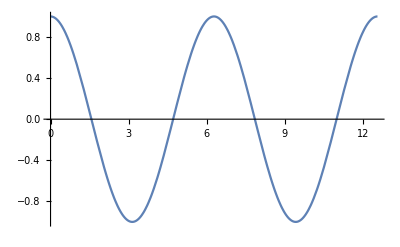

```mathematica
Plot1=Plot[f[t],{t,0,4π}]
```

## Problem 2:

#### Consider a second solution with a different phase and plot both solutions on the same graph.

```mathematica
φ=1
```

1

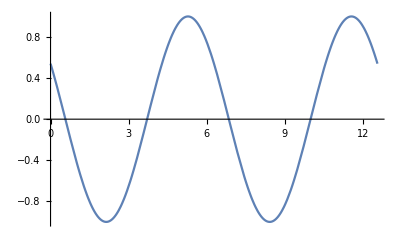

```mathematica
Plot2= Plot[f[t],{t,0,4π}]
```

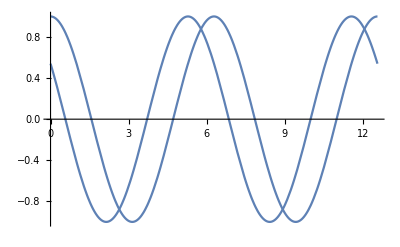

```mathematica
Show[Plot1,Plot2]
```

## Problem 3:

### Consider a third solution with a different period. Compare with the first solution on the same plot.

```mathematica
m=4
k=1
ω=Sqrt[k/m]
```

4

1

1/2

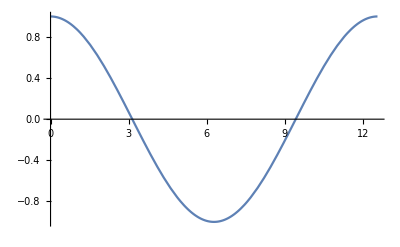

```mathematica
Plot3=Plot[f[t],{t,0,4π}]
```

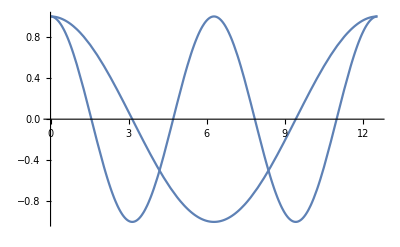

```mathematica
Show[Plot1,Plot3]
```

## Problem 4:

### Define the solution of velocity (v) for a simple harmonic oscillator. Plot v vs. x using [ParametricPlot] and discuss the result.

#### v = x’ = -Aωsin(ωt+φ)

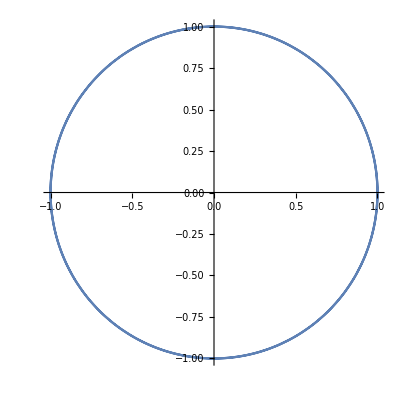

```mathematica
ParametricPlot[{f[t],f'[t]},{t,0,4π}]
```

#### When sin and cosine are plotted against each other parametrically the result will be a circle as long as they have the same argument as is the case with the position and velocity of simple harmonic motion. The radius will represent the amplitude which is constant.

## Problem 5:

### Repeat questions1and 4 for a damped oscillator with underdamping. 5.1

```mathematica
b=.4
ω'=ω*Sqrt[1-(b/(2*m*ω))^2]
B=(b/(2m))
g[t_]:=A*(Exp[-B*t])*Cos[ω'*t+φ]
```

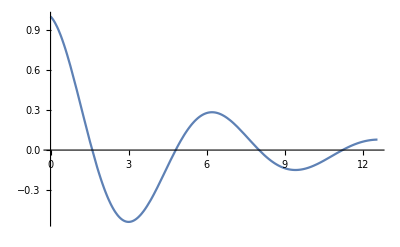

```mathematica
Plot4=Plot[g[t],{t,0,4π}]
```

### 5.2

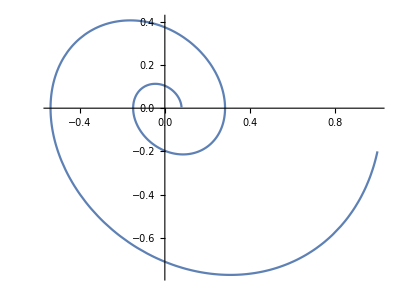

```mathematica
ParametricPlot[{g[t],g'[t]},{t,0,4π}Plot]
```

### This is once again what we’d expect as the radius represents the amplitude of our harmonic motion. As t aproaches 4π the amplitude of both the position and velocity decrease creating a spiral shape.

## Problem 6:

### Investigate 5 new Mathematica commands not covered in the tutorial or in the questions above (perhaps using the Help menu or Schaum’s outline for ideas). Show the results of these commands in your Mathematica notebook.

### 6.1

```mathematica
Beep[]
```

### 6.2

```mathematica
Speak["I can't do that dave"]
```

### 6.3

```mathematica
ChemicalData["Ethanol","MoleculePlot"]
```

-Graphics3D-

### 6.4

```mathematica
Sunset[Here]
```

Tue 6 Sep 2016 19:45GMT-5.

### 6.5

```mathematica
MoonPosition[]
```

{202.78 °,43.89 °}